# Regression

## Linear regression

### Model fitting

Imagine we have some data taken from an experiment and we would like to find a model that fits the data well.

Here is some data I took earlier. Can you figure out a good model for this data? Once you have a good idea for a model, try using Mathematica’s FindFit function to test it with the data. How would you verify that your model is a good fit for the data?

```mathematica
data=;
```

#### Analysis

Here is how I created that mystery data:

The first thing we should do is try to plot the data to see if we can recognise anything

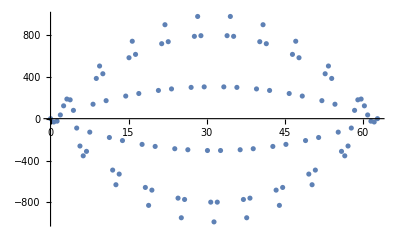

```mathematica
ListPlot[data]
```

If we have a good idea for a model that might fit the data, then we can use FindFit to look for the parameters that best fit the data. This looks like the plot of cos(x) modulated by a quadratic so let’s try to fit a linear model of that form to the data:

```mathematica
fit = FindFit[data, {Mod[cos[x],(ax^2 + bx + c)]}, {a,b,c}, {x}]
fit = FindFit[data, (ax^2 + bx + c)cos[x], {a,b,c}, {x}]
```

FindFit::nrlnum: The function value {Mod[cos[0.],1.+ax^2+bx],31.6193+Mod[cos[0.628319],1.+ax^2+bx],23.911+Mod[cos[1.25664],1.+ax^2+bx],-35.5006+Mod[cos[1.88496],1.+ax^2+bx],-122.645+Mod[cos[2.51327],1.+ax^2+bx],«1»,-180.134+Mod[cos[3.76991],1.+«1»+bx],-79.4188+Mod[cos[4.39823],1.+ax^2+bx],89.7883+Mod[cos[5.02655],1.+ax^2+bx],261.578+Mod[cos[5.65487],1.+ax^2+bx],«91»} is not a list of real numbers with dimensions {101} at {a,b,c} = {1.,1.,1.}.

FindFit[{{0,0},{π/5,-99/100 (1+√5) π^2},{(2 π)/5,-49/25 (-1+√5) π^2},{(3 π)/5,-291/100 (1-√5) π^2},{(4 π)/5,-96/25 (-1-√5) π^2},{π,19 π^2},{(6 π)/5,-141/25 (-1-√5) π^2},{(7 π)/5,-651/100 (1-√5) π^2},{(8 π)/5,-184/25 (-1+√5) π^2},{(9 π)/5,-819/100 (1+√5) π^2},{2 π,-36 π^2},{(11 π)/5,-979/100 (1+√5) π^2},{(12 π)/5,-264/25 (-1+√5) π^2},{(13 π)/5,-1131/100 (1-√5) π^2},{(14 π)/5,-301/25 (-1-√5) π^2},{3 π,51 π^2},{(16 π)/5,-336/25 (-1-√5) π^2},{(17 π)/5,-1411/100 (1-√5) π^2},{(18 π)/5,-369/25 (-1+√5) π^2},{(19 π)/5,-1539/100 (1+√5) π^2},{4 π,-64 π^2},{(21 π)/5,-1659/100 (1+√5) π^2},{(22 π)/5,-429/25 (-1+√5) π^2},{(23 π)/5,-1771/100 (1-√5) π^2},{(24 π)/5,-456/25 (-1-√5) π^2},{5 π,75 π^2},{(26 π)/5,-481/25 (-1-√5) π^2},{(27 π)/5,-1971/100 (1-√5) π^2},{(28 π)/5,-504/25 (-1+√5) π^2},{(29 π)/5,-2059/100 (1+√5) π^2},{6 π,-84 π^2},{(31 π)/5,-2139/100 (1+√5) π^2},{(32 π)/5,-544/25 (-1+√5) π^2},{(33 π)/5,-2211/100 (1-√5) π^2},{(34 π)/5,-561/25 (-1-√5) π^2},{7 π,91 π^2},{(36 π)/5,-576/25 (-1-√5) π^2},{(37 π)/5,-2331/100 (1-√5) π^2},{(38 π)/5,-589/25 (-1+√5) π^2},{(39 π)/5,-2379/100 (1+√5) π^2},{8 π,-96 π^2},{(41 π)/5,-2419/100 (1+√5) π^2},{(42 π)/5,-609/25 (-1+√5) π^2},{(43 π)/5,-2451/100 (1-√5) π^2},{(44 π)/5,-616/25 (-1-√5) π^2},{9 π,99 π^2},{(46 π)/5,-621/25 (-1-√5) π^2},{(47 π)/5,-2491/100 (1-√5) π^2},{(48 π)/5,-624/25 (-1+√5) π^2},{(49 π)/5,-2499/100 (1+√5) π^2},{10 π,-100 π^2},{(51 π)/5,-2499/100 (1+√5) π^2},{(52 π)/5,-624/25 (-1+√5) π^2},{(53 π)/5,-2491/100 (1-√5) π^2},{(54 π)/5,-621/25 (-1-√5) π^2},{11 π,99 π^2},{(56 π)/5,-616/25 (-1-√5) π^2},{(57 π)/5,-2451/100 (1-√5) π^2},{(58 π)/5,-609/25 (-1+√5) π^2},{(59 π)/5,-2419/100 (1+√5) π^2},{12 π,-96 π^2},{(61 π)/5,-2379/100 (1+√5) π^2},{(62 π)/5,-589/25 (-1+√5) π^2},{(63 π)/5,-2331/100 (1-√5) π^2},{(64 π)/5,-576/25 (-1-√5) π^2},{13 π,91 π^2},{(66 π)/5,-561/25 (-1-√5) π^2},{(67 π)/5,-2211/100 (1-√5) π^2},{(68 π)/5,-544/25 (-1+√5) π^2},{(69 π)/5,-2139/100 (1+√5) π^2},{14 π,-84 π^2},{(71 π)/5,-2059/100 (1+√5) π^2},{(72 π)/5,-504/25 (-1+√5) π^2},{(73 π)/5,-1971/100 (1-√5) π^2},{(74 π)/5,-481/25 (-1-√5) π^2},{15 π,75 π^2},{(76 π)/5,-456/25 (-1-√5) π^2},{(77 π)/5,-1771/100 (1-√5) π^2},{(78 π)/5,-429/25 (-1+√5) π^2},{(79 π)/5,-1659/100 (1+√5) π^2},{16 π,-64 π^2},{(81 π)/5,-1539/100 (1+√5) π^2},{(82 π)/5,-369/25 (-1+√5) π^2},{(83 π)/5,-1411/100 (1-√5) π^2},{(84 π)/5,-336/25 (-1-√5) π^2},{17 π,51 π^2},{(86 π)/5,-301/25 (-1-√5) π^2},{(87 π)/5,-1131/100 (1-√5) π^2},{(88 π)/5,-264/25 (-1+√5) π^2},{(89 π)/5,-979/100 (1+√5) π^2},{18 π,-36 π^2},{(91 π)/5,-819/100 (1+√5) π^2},{(92 π)/5,-184/25 (-1+√5) π^2},{(93 π)/5,-651/100 (1-√5) π^2},{(94 π)/5,-141/25 (-1-√5) π^2},{19 π,19 π^2},{(96 π)/5,-96/25 (-1-√5) π^2},{(97 π)/5,-291/100 (1-√5) π^2},{(98 π)/5,-49/25 (-1+√5) π^2},{(99 π)/5,-99/100 (1+√5) π^2},{20 π,0}},{Mod[cos[x],ax^2+bx+c]},{a,b,c},{x}]

```mathematica
ListPlot[fit[[1]]]
```

FindFit::nrlnum: The function value {Mod[0.,1.+ax^2+bx],31.6193+Mod[0.628319 cos,1.+ax^2+bx],23.911+Mod[1.25664 cos,1.+ax^2+bx],-35.5006+Mod[1.88496 cos,1.+ax^2+bx],-122.645+Mod[2.51327 cos,1.+ax^2+bx],-«18»+Mod[«1»,«1»],-180.134+Mod[3.76991 cos,1.+ax^2+bx],-79.4188+Mod[4.39823 cos,1.+ax^2+bx],89.7883+Mod[5.02655 cos,1.+ax^2+bx],261.578+Mod[5.65487 cos,1.+ax^2+bx],«91»} is not a list of real numbers with dimensions {101} at {a,b,c} = {1.,1.,1.}.

-Graphics-

Now we plot the model against the data

Now that we have seen a simple example, let’s apply what we have learned in the lectures to see if we can reproduce this and in the process understand what Mathematica has done to find a good fit to the data.

### Linear Regression for a linear function

We will start with a simple problem: find the line that best fits some data by determining the best fit parameters (α, β) in our model f(x)=α+β x.

The first thing we need is to collect some data samples. Normally, this could come from some experimental measurements, but for this example we will just generate some data ourselves.  In the real world we will never have perfectly clean measurements so we will expect some random noise in our samples. To simulate this, we will add some random noise when we’re generating the data we want to fit.

Now the first column are the values of x_i and the second column is f(x_i). Let’s extract those two columns from the matrix.

The next thing we need to do is build up the matrix A representing our model evaluated for each value of x_i

Our model is then A(α
β)=f(x_i). The matrix A is an example where we have many rows but only two columns, so this is an over-constrained problem. As such we won’t be able to find a perfect solution (f(x_i) is not in the column space of A!), so we will look for a solutions that minimises ||A(α
β)=f(x_i)||. We saw how to do this in our linear algebra examples, where we had three ways to find the best fit solution:

#### Method 1: Directly minimise ||A(α β)=f(x_i)||

We can numerically search for the minimum over the parameters α and β. This is an example of an unconstrained convex optimisation problem

We now check visually that we have indeed found the minimum:

This is equivalent to solving A^T A x̂=A^T f(x_i), i.e. using using A^Tto project onto the column space of A . Note that (A^T A)^-1 exists when A has independent columns [N(A) = N(A^T A)].

#### Method 2: QR

Recall that we saw that we could solve A^T A x̂=A^T f(x_i) efficiently if we had the QR decomposition of A. We have A^T A=(Q R)^T(QR) = R^T Q^T Q R=R^T R and A^T f(x_i)=(Q R)^T f(x_i)=R^T Q^T f(x_i) so our problem reduces to R x̂=Q^T b.

#### Method 3: Pseudoinverse

Our third approach is to use the pseudoinverse to solve the problem directly.

We could also this using the singular value decomposition

#### Method 4: Gradient descent

### Overfitting and under-fitting

We might think that we could obtain a better fit by introducing more parameters into our model. Similarly we might think that we could save some time by using fewer parameters. While this might be true in some cases, in many cases  it leads to problems of overfitting and under-fitting, respectively. Let’s use Mathematica’s Fit to fit three models to the data, one with too few parameters, one with two many, and one with the correct number

The green curve representing a 10th order polynomial certainly fits the blue points better (it exactly passes through them all - interpolation!) but it is clearly a worse fit than the orange. We have overfit our model. We could check for this by adding another point (which was not used in the training) and checking if it fits the model.

Similarly, the blue line (0th order polynomial) is an underfit and is not a good model for the data.

### Linear Regression for a nonlinear function (but still linear in parameters)

There is nothing in linear regression that assumes our model must be a liner function of the variables. Let’s try it with a nonlinear function

### Linear Regression in multiple dimensions

It is straightforward to generalise to data in multiple dimensions:

## Nonlinear regression

We haven’t covered it in the lectures, but we can also fit a non-linear model, where we have a non-linear function of the parameters. To start, let’s make up some data to use:

We can fit a nonlinear model to this data

Now we plot the model against the data to check it does fit

## Logistic regression

Finally, let’s look at an example of Logistic Regression. We will return to the MNIST Digits dataset we studied using Principal Component Analysis.

To save time, we will train the model using a subset of the data.

We could use LogitModelFit to fit a model and then used that to build a function that takes in an image and returns a number, but rather than worrying about the messy details we can use Classify with the LogisticRegression method specified. This takes care of converting the image to a matrix and all the other messy details.

We can now treat this as a function that takes in an image and returns a number. Let’s look at some information about the function:

Let’s see how well it performs by testing it on a random sample of the test data

It’s right about 2/3 of the time. We could improve this by going back to the training step and using more training samples:

Now this is close to 90% accurate